# Aula 03 - Introdução à Física Computacional I

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.sousa@usp.br

## 1.

Dadas as matrizes A e B a seguir, expresse-as como uma lista de listas, determine o produto matricial AB e exiba o resultado na forma matricial:
A = (1
00
2-1
3),  B = (2 | -1 | 4
1 | 0 | -2
0 | 3 | 1)
(Resposta: A B = (2
2-4
93
-1)

```mathematica
(*Expressando a lista A*)
A = {{1, 0, -1},{0, 2, 3}}
```

{{1,0,-1},{0,2,3}}

```mathematica
(*Expressando a lista B*)
B ={{2, -1, 4}, { 1, 0, -2}, { 0, 3, 1}}
```

{{2,-1,4},{1,0,-2},{0,3,1}}

```mathematica
A.B//MatrixForm
```

(2 | -4 | 3
2 | 9 | -1)

## 2.

Em um planeta distante, astronautas lançam uma pedra no ar. Com a ajuda de uma câmera que tira fotos a intervalos de tempo regulares, eles registram a altura da pedra como função do tempo, obtendo os dados mostrados na tabela abaixo.

-Graphics-

• Com a função Table, ou seja, sem digitar diretamente os valores, faça uma lista dos tempos t_i associados a cada medida..

```mathematica
t = Table[N[(n-1)/4],{n,21}]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

• Defina uma lista simples com os dados da altura y_i da pedra nos diversos instantes.

```mathematica
y = {5, 5.75, 6.4, 6.94, 7.38, 7.72, 7.96, 8.1, 8.13, 8.07, 7.9, 7.62, 7.25, 6.77, 6.2, 5.52, 4.73, 3.85, 2.86, 1.77, 0.58}
```

{5,5.75,6.4,6.94,7.38,7.72,7.96,8.1,8.13,8.07,7.9,7.62,7.25,6.77,6.2,5.52,4.73,3.85,2.86,1.77,0.58}

• Com a função Transpose, faça uma lista de pares ordenados {t_i ,  y_i}.

```mathematica
yt = Transpose[{ t, y}]
```

{{0.,5},{0.25,5.75},{0.5,6.4},{0.75,6.94},{1.,7.38},{1.25,7.72},{1.5,7.96},{1.75,8.1},{2.,8.13},{2.25,8.07},{2.5,7.9},{2.75,7.62},{3.,7.25},{3.25,6.77},{3.5,6.2},{3.75,5.52},{4.,4.73},{4.25,3.85},{4.5,2.86},{4.75,1.77},{5.,0.58}}

• Com a função ListPlot, faça o gráfico da altura em função do tempo.

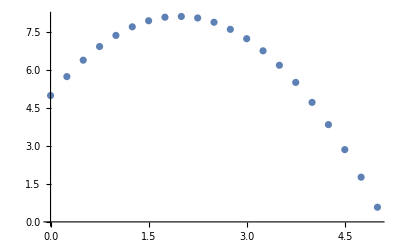

```mathematica
ListPlot[yt]
```